```mathematica
ShiftSparse[t_]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
CoinSparse[t_]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[FourierMatrix[2]]]

USparse[t_]:=ShiftSparse[t].CoinSparse[t]
```

```mathematica
ShiftSparse[1]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0
1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
xc=yu=75;
HorizontalBoundary[y_]:=Round[xc+Sqrt[xc^2-y^2]]
VerticalBoundary[x_]:=Round[Sqrt[yu^2-(x^2-xc)]]
```

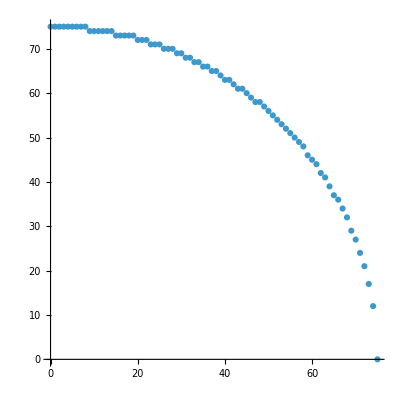

```mathematica
(*y*)
r=75;
ListPlot[{#,Round[Sqrt[r^2-#^2]]}&/@Range[r,0,-1.],AspectRatio->1]
```

```mathematica
{#,VerticalBoundary[#]}&/@Range[0,2*xc]
```

{{0,75},{1,75},{2,75},{3,75},{4,75},{5,75},{6,75},{7,75},{8,75},{9,75},{10,75},{11,75},{12,75},{13,74},{14,74},{15,74},{16,74},{17,74},{18,73},{19,73},{20,73},{21,73},{22,72},{23,72},{24,72},{25,71},{26,71},{27,71},{28,70},{29,70},{30,69},{31,69},{32,68},{33,68},{34,67},{35,67},{36,66},{37,66},{38,65},{39,65},{40,64},{41,63},{42,63},{43,62},{44,61},{45,61},{46,60},{47,59},{48,58},{49,57},{50,57},{51,56},{52,55},{53,54},{54,53},{55,52},{56,51},{57,50},{58,48},{59,47},{60,46},{61,44},{62,43},{63,42},{64,40},{65,38},{66,37},{67,35},{68,33},{69,31},{70,28},{71,26},{72,23},{73,19},{74,15},{75,9},{76,9 ⅈ},{77,15 ⅈ},{78,20 ⅈ},{79,23 ⅈ},{80,26 ⅈ},{81,29 ⅈ},{82,32 ⅈ},{83,34 ⅈ},{84,37 ⅈ},{85,39 ⅈ},{86,41 ⅈ},{87,43 ⅈ},{88,45 ⅈ},{89,47 ⅈ},{90,49 ⅈ},{91,51 ⅈ},{92,53 ⅈ},{93,54 ⅈ},{94,56 ⅈ},{95,58 ⅈ},{96,59 ⅈ},{97,61 ⅈ},{98,62 ⅈ},{99,64 ⅈ},{100,66 ⅈ},{101,67 ⅈ},{102,69 ⅈ},{103,70 ⅈ},{104,72 ⅈ},{105,73 ⅈ},{106,74 ⅈ},{107,76 ⅈ},{108,77 ⅈ},{109,79 ⅈ},{110,80 ⅈ},{111,81 ⅈ},{112,83 ⅈ},{113,84 ⅈ},{114,85 ⅈ},{115,87 ⅈ},{116,88 ⅈ},{117,89 ⅈ},{118,91 ⅈ},{119,92 ⅈ},{120,93 ⅈ},{121,95 ⅈ},{122,96 ⅈ},{123,97 ⅈ},{124,98 ⅈ},{125,100 ⅈ},{126,101 ⅈ},{127,102 ⅈ},{128,103 ⅈ},{129,105 ⅈ},{130,106 ⅈ},{131,107 ⅈ},{132,108 ⅈ},{133,109 ⅈ},{134,111 ⅈ},{135,112 ⅈ},{136,113 ⅈ},{137,114 ⅈ},{138,116 ⅈ},{139,117 ⅈ},{140,118 ⅈ},{141,119 ⅈ},{142,120 ⅈ},{143,121 ⅈ},{144,123 ⅈ},{145,124 ⅈ},{146,125 ⅈ},{147,126 ⅈ},{148,127 ⅈ},{149,128 ⅈ},{150,130 ⅈ}}

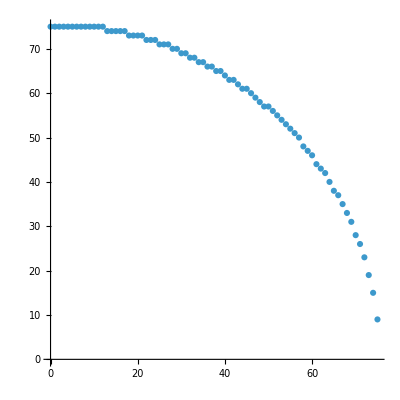

```mathematica
ListPlot[{#,VerticalBoundary[#]}&/@Range[0,2*xc],AspectRatio->1,PlotRange->Full]
```

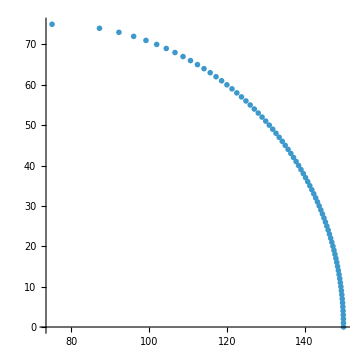
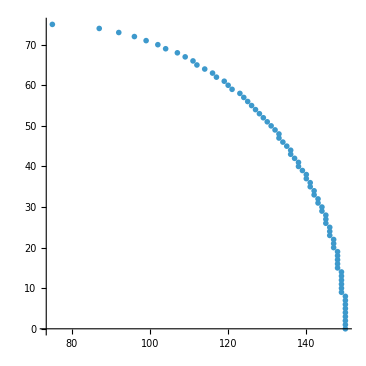

```mathematica
xc=75;
{ListPlot[{xc+Sqrt[xc^2-#^2],#}&/@Range[0,xc],AspectRatio->1],ListPlot[{Round[xc+Sqrt[xc^2-#^2]],#}&/@Range[0,xc],AspectRatio->1]}
```